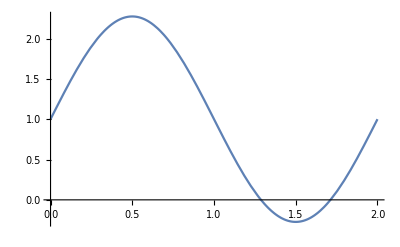

```mathematica
Plot[1+4/Pi*Sum[Sin[(2*n+1)*Pi*t]/(2*n+1),{n,0,0,1}],{t,0,2}]
```

```mathematica
f:=2/;0≤t≤1;
f:=0/;1<t≤2;
```

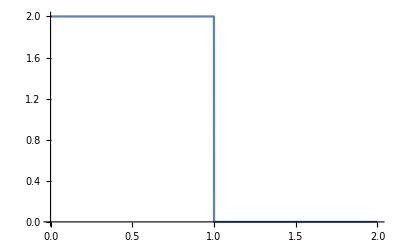

```mathematica
Plot[f,{t,0,2}]
```

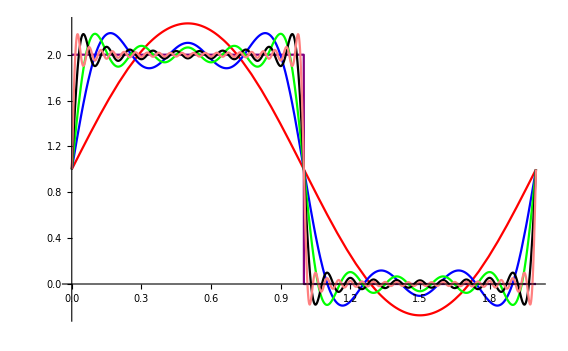

```mathematica
Plot[{f,
1+4/Pi*Sum[Sin[(2*n+1)*Pi*t]/(2*n+1),{n,0,0,1}],1+4/Pi*Sum[Sin[(2*n+1)*Pi*t]/(2*n+1),{n,0,2,1}],1+4/Pi*Sum[Sin[(2*n+1)*Pi*t]/(2*n+1),{n,0,4,1}],
1+4/Pi*Sum[Sin[(2*n+1)*Pi*t]/(2*n+1),{n,0,9,1}],
1+4/Pi*Sum[Sin[(2*n+1)*Pi*t]/(2*n+1),{n,0,19,1}]},{t,0,2},PlotStyle->{Purple,Red,Blue,Green,Black,Pink}]
```